```mathematica
JUAN FRANCISCO ABÁN FONTECHA
DNI: 77365843F
MATEMATICAS DISCRETAS
Dia: 17-11-2014
```

```mathematica
RETICULO[A_,R_]:=Module[{reticulo,cotassuperiores,cotasinferiores,csuper,cinfer,supremo,infimo,mini,maxi,m,n,x1,x2},reticulo=True;Do[
Do[
cotassuperiores={};cotasinferiores={};Do[csuper=True;cinfer=True;If[Intersection[{{A[[x1]],A[[n]]}},R]=={},csuper=False];If[Intersection[{{A[[x2]],A[[n]]}},R]=={},csuper=False];If[Intersection[{{A[[n]],A[[x1]]}},R]=={},cinfer=False];If[Intersection[{{A[[n]],A[[x2]]}},R]=={},cinfer=False];If[csuper,AppendTo[cotassuperiores,A[[n]]]];If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];supremo={};infimo={};
Do[mini=True;Do[If[Intersection[{{cotassuperiores[[n]],cotassuperiores[[m]]}},R]=={},mini=False],{m,1,Length[cotassuperiores]}];If[mini,AppendTo[supremo,cotassuperiores[[n]]]];,{n,1,Length[cotassuperiores]}];If[supremo=={},reticulo=False];Do[maxi=True;
Do[If[Intersection[{{cotasinferiores[[m]],cotasinferiores[[n]]}},R]=={},maxi=False],{m,1,Length[cotasinferiores]}];If[maxi,AppendTo[infimo,cotasinferiores[[n]]]];,{n,1,Length[cotasinferiores]}];If[infimo=={},reticulo=False];,{x1,1,Length[A]}];,{x2,1,Length[A]}];reticulo]
```

```mathematica
ORDEN[A_,R_]:=Module[{Reflexiva,Antisimetrica,Transitiva,n,p,q,r},Reflexiva=True;For[n=1,n≤Length[A],n++,If[Intersection[{{A[[n]],A[[n]]}},R]=={{A[[n]],A[[n]]}},Null,Reflexiva=False]];
Transitiva=True;
For[p=1,p≤Length[R],p++,For[q=1,q≤Length[R],q++,If[R[[p,1]]==R[[q,2]],If[Intersection[{{R[[q,1]],R[[p,2]]}},R]=={{R[[q,1]],R[[p,2]]}},Null,Transitiva=False]];];];
Antisimetrica=True;
For[r=1,r≤Length[R],r++,If[Intersection[{{R[[r,2]],R[[r,1]]}},R]=={{R[[r,2]],R[[r,1]]}}&&!(ToString[R[[r,1]]]==ToString[R[[r,2]]]),Antisimetrica=False]];
If[Reflexiva&&Antisimetrica&&Transitiva,True,False]]
```

```mathematica
COMPLEMENTO[A_,R_,n_]:=Module[{complemento,k},
complemento={};
Do[If[INFIMO[A,{A[[k]],n},R]==MINIMALES[A,R]&&SUPREMO[A,{A[[k]],n},R]==MAXIMALES[A,R],AppendTo[complemento,A[[k]]]],{k,1,Length[A]}];
complemento]
```

```mathematica
COMPLEMENTADO[A_,R_]:=Module[{complementado,k},complementado=True;
Do[If[COMPLEMENTO[A,R,A[[k]]]=={},complementado=False],{k,1,Length[A]}];
complementado]
```

```mathematica
RETICULODISTRIBUTIVO[A_,R_]:=Module[{distributivo,i,j,k},distributivo=True;
Do[Do[Do[If[TrueQ[SUPREMO[A,Union[{A[[i]]},INFIMO[A,{A[[j]],A[[k]]},R]],R]==INFIMO[A,Union[SUPREMO[A,{A[[i]],A[[j]]},R],SUPREMO[A,{A[[i]],A[[k]]},R]],R]],,distributivo=False;];,{i,1,Length[A]}];,{j,1,Length[A]}];,{k,1,Length[A]}];
distributivo]
```

```mathematica
MAXIMO[A_,R_]:=Module[{maximo,maxi,n,m},maximo={};
Do[maxi=True;
Do[If[Intersection[{{A[[m]],A[[n]]}},R]=={},maxi=False],{m,1,Length[A]}];
If[maxi,AppendTo[maximo,A[[n]]]];,{n,1,Length[A]}];
maximo]
```

```mathematica
MINIMO[A_,R_]:=Module[{minimo,mini,m,n},minimo={};
Do[mini=True;
Do[If[Intersection[{{A[[n]],A[[m]]}},R]=={},mini=False],{m,1,Length[A]}];
If[mini,AppendTo[minimo,A[[n]]]];,{n,1,Length[A]}];
minimo]
```

```mathematica
MAXIMALES[A_,R_]:=Module[{maximales,maximal,m,n},maximales={};
Do[maximal=True;
Do[If[Intersection[{{A[[n]],A[[m]]}},R]≠{}&&n≠m,maximal=False],{m,1,Length[A]}];
If[maximal,AppendTo[maximales,A[[n]]]];,{n,1,Length[A]}];
maximales]
```

```mathematica
MINIMALES[A_,R_]:=Module[{minimales,minimal,m,n},minimales={};
Do[minimal=True;
Do[If[Intersection[{{A[[m]],A[[n]]}},R]≠{}&&n≠m,minimal=False],{m,1,Length[A]}];
If[minimal,AppendTo[minimales,A[[n]]]];,{n,1,Length[A]}];
minimales]
```

```mathematica
COTASSUPERIORES[A_,B_,R_]:=Module[{cotassuperiores,csuper,m,n},cotassuperiores={};
Do[csuper=True;
Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False],{m,1,Length[B]}];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];
cotassuperiores]
```

```mathematica
COTASINFERIORES[A_,B_,R_]:=Module[{cotasinferiores,cinfer,m,n},cotasinferiores={};
Do[cinfer=True;
Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False],{m,1,Length[B]}];
If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
cotasinferiores]
```

```mathematica
SUPREMO[A_,B_,R_]:=Module[{cotassuperiores,csuper,supremo,mini,m,n},cotassuperiores={};
Do[csuper=True;
Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False],{m,1,Length[B]}];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];
supremo={};
Do[mini=True;
Do[If[Intersection[{{cotassuperiores[[n]],cotassuperiores[[m]]}},R]=={},mini=False],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]]];,{n,1,Length[cotassuperiores]}];
supremo]
```

```mathematica
INFIMO[A_,B_,R_]:=Module[{cotasinferiores,cinfer,infimo,maxi,m,n},cotasinferiores={};
Do[cinfer=True;
Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False],{m,1,Length[B]}];
If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
infimo={};
Do[maxi=True;
Do[If[Intersection[{{cotasinferiores[[m]],cotasinferiores[[n]]}},R]=={},maxi=False],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]]];,{n,1,Length[cotasinferiores]}];
infimo]
```

### 8. Se considera el conjunto A = {a, b, c, d} y en él, la relación binaria R = {(d, d), (d, c), (d, b), (d, a), (c, c), (c, b), (c, a), (b, b), (b, a), (a, a)} ¿Es A un retículo?

{a,b,c,d}

{{d,d},{d,c},{d,b},{d,a},{c,c},{c,b},{c,a},{b,b},{b,a},{a,a}}

```mathematica
A={a,b,c,d}
R={{d,d},{d,c},{d,b},{d,a},{c,c},{c,b},{c,a},{b,b},{b,a},{a,a}}

RETICULO[A,R]
```

{a,b,c,d}

{{d,d},{d,c},{d,b},{d,a},{c,c},{c,b},{c,a},{b,b},{b,a},{a,a}}

True

```mathematica
¿Es A con las operaciones anteriores un álgebra de Boole?
```

```mathematica
ORDEN[A,R]
```

True

```mathematica
COMPLEMENTADO[A,R]
```

False

```mathematica
RETICULODISTRIBUTIVO[A,R]
```

True

General::obspkg: "Graphics`Arrow`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

Diagrama de orden:

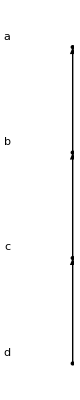

```mathematica
<<Graphics`Arrow`
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];B=A;t1=1;nivel=0;While[B≠{},minimales={};nivel++;Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False],{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,
{n1,1,Length[B]}];
B=Complement[B,minimales];
]
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];R1={};
Do[
Do[
If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,
R1=Union[R1,{R[[k1]]}];
];
,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];Do[t1++;puntos=Union[puntos,{Text[tabla[[t1,2]],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2),{k1,1,cont}],
{j1,1,tabla[[Length[A],1]]}];Coord[elem_]:=Do[If[elem==tabla[[h1,2]],
Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];Do[Coord[A[[i1]]],{i1,1,Length[A]}];Do[AppendTo[puntos,Arrow[Coord[R[[t1,1]]],Coord[R[[t1,2]]]]];
,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos]]
```

```mathematica
No es Un Algebra de Boole
```

### 9. Sea D el conjunto de los números que son divisores positivos de 70. En D se considera la relación de orden dada por : a <= b ⇔ a divide a b

```mathematica
A={1,2,5,7,10,14,35,70}
R={{1,1},{1,2},{1,5},{1,7},{1,10},{1,14},{1,35},{1,70},{2,2},{2,10},{2,14},{2,70},{5,5},{5,10},{5,35},{5,70},{7,7},{7,14},{7,35},{7,70},{10,10},{10,70},{14,14},{14,70},{35,35},{35,70},{70,70}};
```

{1,2,5,7,10,14,35,70}

#### ¿Tiene (D, <=) estructura de retículo?¿Es distributivo?¿Es complementado?¿Es un álgebra de Boole?En caso afirmativo ¿quiénes son sus átomos?

```mathematica
RETICULO[A,R]
```

True

```mathematica
RETICULODISTRIBUTIVO[A,R]
```

True

```mathematica
MAXIMALES[A,R]
```

{70}

```mathematica
MINIMALES[A,R]
```

{1}

```mathematica
COMPLEMENTO[A,R,1]
```

{70}

```mathematica
COMPLEMENTADO[A,R]
```

True

General::obspkg: "Graphics`Arrow`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

Diagrama de orden:

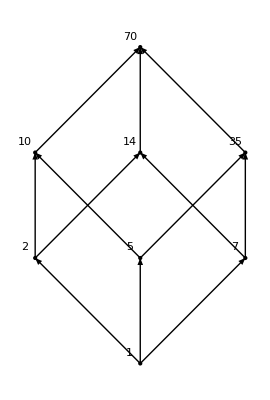

```mathematica
<<Graphics`Arrow`
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];B=A;t1=1;nivel=0;While[B≠{},minimales={};nivel++;Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False],{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,
{n1,1,Length[B]}];
B=Complement[B,minimales];
]
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];R1={};
Do[
Do[
If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,
R1=Union[R1,{R[[k1]]}];
];
,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];Do[t1++;puntos=Union[puntos,{Text[tabla[[t1,2]],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2),{k1,1,cont}],
{j1,1,tabla[[Length[A],1]]}];Coord[elem_]:=Do[If[elem==tabla[[h1,2]],
Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];Do[Coord[A[[i1]]],{i1,1,Length[A]}];Do[AppendTo[puntos,Arrow[Coord[R[[t1,1]]],Coord[R[[t1,2]]]]];
,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos]]
```

```mathematica
Por tanto tenemos un retículo isomorfo a Subscript[𝔹, 2]^3 y en consecuencia es un álgebra de Boole.
```

### 21. Sean A = {a, b} y B = {x, z}. a.Calcular A*B y comprobar que X1 = (A*B), con la relación de orden dada por la inclusión, es un retículo y un álgebra de Boole.

```mathematica
A={a,b};
B={x,z};
cadena="";
For[j=1,j≤Length[A],j++,For[k=1,k≤Length[B],k++,cadena1=StringJoin["{",ToString[A[[j]]],",",ToString[B[[k]]],"}"];
If[j≠1||k≠1,cadena=StringJoin[cadena,","]];
cadena=StringJoin[cadena,cadena1]]];
Print["A = ",A]
Print["B = ",B]
Cartesiano=ToExpression[StringJoin["{",cadena,"}"]]
```

A = {a,b}

B = {x,z}

{{a,x},{a,z},{b,x},{b,z}}

```mathematica
Calcular Partes, hallar relacion de las partes y comprobamos si Partes de AxB es Algebra de Boole
```

```mathematica
A={{a,x},{a,z},{b,x},{b,z}}
R= {{{a,x},{a,x}},{{a,x},{a,z}}, {{a,x},{b,x}},{{a,x},{b,x}},{{a,z},{a,z}},{{a,z},{b,x}},{{a,z},{b,z}},{{b,x},{b,x}},{{b,x},{b,z}},{{b,z},{b,z}}}
RETICULO[A,R]
```

{{a,x},{a,z},{b,x},{b,z}}

{{{a,x},{a,x}},{{a,x},{a,z}},{{a,x},{b,x}},{{a,x},{b,x}},{{a,z},{a,z}},{{a,z},{b,x}},{{a,z},{b,z}},{{b,x},{b,x}},{{b,x},{b,z}},{{b,z},{b,z}}}

False

```mathematica
<<Graphics`Arrow`
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];B=A;t1=1;nivel=0;While[B≠{},minimales={};nivel++;Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False],{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,
{n1,1,Length[B]}];
B=Complement[B,minimales];
]
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];R1={};
Do[
Do[
If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,
R1=Union[R1,{R[[k1]]}];
];
,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];Do[t1++;puntos=Union[puntos,{Text[tabla[[t1,2]],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2),{k1,1,cont}],
{j1,1,tabla[[Length[A],1]]}];Coord[elem_]:=Do[If[elem==tabla[[h1,2]],
Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];Do[Coord[A[[i1]]],{i1,1,Length[A]}];Do[AppendTo[puntos,Arrow[Coord[R[[t1,1]]],Coord[R[[t1,2]]]]];
,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos]]
```

Get::noopen: Cannot open "Graphics`Arrow`".

$Failed

Diagrama de orden:

-Graphics-

### b.Calcular X2 = (A)*(B) y comprobar que, con la relación de orden dada por la inclusión, es un retículo y un álgebra de Boole.c.¿Son X1 y X2 retículos isomorfos?